# SEMINARSKA NALOGA STATISTIKA KASAŠKIH DIRK

## Andreja Lapajne, praktična matematika, FMF, UL

```mathematica
Import["kasaske-dirke.jpg"]
```

-Graphics-

# UVOD

Za seminarsko nalogo pri predmetu računalniška orodja v matematiki (ROM) sem si izbrala statistično obdelavo kasaških dirk. Na spleti strani  http://www.zveza-kasaska-centrala.si/ (spodaj je aktivna povezava do spletne strani) sem zbrala podatke 26 kobil in primerjala izpisane podatke za sezono 2018 v tabele.
Primerjala sem starost kobil, število nastopov v sezoni ter uvrstitev na prvo, drugo in tretje mesto.

```mathematica
Hyperlink["http://www.zveza-kasaska-centrala.si/"]
```

http://www.zveza-kasaska-centrala.si/

# O kasaških dirkah

## KASAŠTVO IN DIRKE

Kasaštvo je konjeniška disciplina, kjer konj tekmuje v splecifičnem hodu - kasu. Konji - kasači - vlečejo poseben dvokolesni voz, imenovan sulki, v Evropi pa so razširjene tudi dirke v kasu pod sedlom. 

Konji so glede na starost in denarsni zaslužek razdeljenji v različne dirke. Mlajši konji z nižjim zaslužkom imajo nižji denarni sklad, med bolj izkušenimi konji je konkurenca hujša, posledično pa so večje tudi denarne nagrade. Nagradni sklad Prix d’Ameriqua je milijon evrorv, na hipodromu Vincennes pa se zbere več kot štirideset tisoč obiskovalcev. 
Vozniki morajo nositi drese, čelado, primerno obutev, priporočljiva so tudi zaščitna očala in rokavice.

## KAS PRI NAS

Kasaštvo je najbolj razvita konjeniška disciplina pri nas, še posebej razvito je v Prlekiji, kjer so bile leta 1874 prve konjske dirke, leto kasneje pa je bilo ustanovljeno dirkalno društvo. Tu že stoletja vzrejajo ljutomerskega kasača, njegov živahen temperament pa je uporaben tudi v gospodarstvu. Kasaški klub Ljutomer na leto organizira od osem do deset dirk, nedeljski popoldnevi so tu že tradicionalno rezervirani za kasaške dirke. Drugi center kasaštva je Ljubljana, hipodromi pa so tudi v Komendi, Krškem, Lenartu v Slovenskih goricah, Šentjerneju, Krimu in Mariboru.

# Definirane funkcije za statistično obdelavo podatkov

OBLIKOVANA TABELA

LEGENDA TABELE

```mathematica
Legenda[tabela_] := First[First[tabela]]
```

VSI PODATKI TABELE

```mathematica
VsiPodatki[tabela_]:= First[tabela]
```

VSI PODATKI BREZ LEGENDE

```mathematica
PodatkiBrez[tabela_] := Rest[First[tabela]]
```

INDEKS STOLPCA TABELE

```mathematica
IndeksStolpca[tabela_,stolpec_] := Position[Legenda[tabela],stolpec]//First // First
```

PODATKI V DANEM STOLPCU

```mathematica
VrednostStolpca[tabela_,stolpec_]:= Transpose[PodatkiBrez[tabela]][[IndeksStolpca[tabela, stolpec]]]
```

POVPREČJE

```mathematica
Povprecje[tabela_,stolpec_]:= Mean[VrednostStolpca[tabela, stolpec]]
```

MAKSIMALNA VREDNOST

```mathematica
MaxVrednost[tabela_, stolpec_] := Max[VrednostStolpca[tabela, stolpec]]
```

MINIMALNA VREDNOST

```mathematica
MinVrednost[tabela_, stolpec_] := Min[VrednostStolpca[tabela, stolpec]]
```

PODATEK IN MAKSIMALNA VREDNOST

```mathematica
maksimalniPodatek[tabela_,prviStolpec_,drugiStolpec_]:= MaximalBy[Transpose[{VrednostStolpca[tabela,prviStolpec],VrednostStolpca[tabela, drugiStolpec]}],Last]
```

PODATEK IN MINIMALNA VREDNOST

```mathematica
minimalniPodatek[tabela_,prviStolpec_,drugiStolpec_]:= MaximalBy[Transpose[{VrednostStolpca[tabela,prviStolpec],VrednostStolpca[tabela, drugiStolpec]}],Last]
```

RISANJE GRAFOV

```mathematica
graf[tabela_,stolpec_,stolpec1_]:=BarChart[{VrednostStolpca[tabela, stolpec]},ChartStyle->RGBColor[0.,0.57,0.18,0.5],ChartLegends->{VrednostStolpca[tabela, stolpec1]}]
```

LINIJSKI PRIKAZ VREDNOSTI

```mathematica
LinijskiPrikaz[tabela_,stolpec_]:= NumberLinePlot[{VrednostStolpca[tabela,stolpec]}]
```

# Statistika starosti kobil ter njihovi nastopi v letu 2018

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Lapajne\Documents\faks\1.pra\rom\projekt

```mathematica
tabela1 = TableForm[Import["podatki.xlsx",{"Sheets","tabela1"}]]
```

ime kobile | starost | število nastopov v 2018 | celotno število štartov | uvrstitev na 1. mesto | uvrstitev na 2. mesto | uvrstitev na 3. mesto
ROMI MMS (IT) | 8. | 15. | 74. | 26. | 7. | 10.
PAOLENDRY LIKE (IT) | 9. | 13. | 23. | 3. | 6. | 3.
PETERKA I  | 4. | 15. | 31. | 10. | 2. | 3.
EROS JOSSELYN(FR) | 4. | 8. | 9. | 7. | 1. | 0.
DELUX MS | 6. | 3. | 28. | 16. | 1. | 1.
VILA AND GLORY (IT) | 4. | 13. | 26. | 7. | 3. | 6.
TARS STARS | 7. | 14. | 65. | 17. | 19. | 11.
DIDIER BLEU | 4. | 16. | 30. | 13. | 9. | 5.
ZAGABRIA VANI (IT) | 3. | 7. | 11. | 2. | 5. | 0.
ROADY DEL SILE(IT) | 8. | 15. | 89. | 16. | 18. | 9.
NARCIS PEŠKI | 7. | 11. | 51. | 21. | 8. | 7.
UNICA SPRIZT(IT) | 5. | 9. | 11. | 0. | 1. | 0.
ORIZZONTE TRIO (IT) | 10. | 6. | 20. | 5. | 0. | 4.
VIRGINIA BABA/IT) | 4. | 13. | 28. | 4. | 7. | 5.
SAMMI MS | 7. | 1. | 48. | 21. | 8. | 4.
THE WAY OF NANDO(IT) | 6. | 3. | 26. | 8. | 4. | 1.
VERA LIGHT(IT) | 4. | 9. | 9. | 0. | 2. | 0.
VITTORINA JET(IT) | 4. | 19. | 29. | 9. | 7. | 3.
BEAR GLIDE(SE) | 8. | 13. | 55. | 10. | 10. | 7.
ROŽLE | 6. | 12. | 43. | 13. | 4. | 7.
ISKRA KP | 4. | 10. | 22. | 4. | 4. | 3.
APOLLO | 9. | 6. | 83. | 12. | 14. | 9.
VANILLA MMS (IT) | 4. | 10. | 23. | 7. | 5. | 1.
PALMARIVATEKIHOVA (IT) | 9. | 10. | 12. | 1. | 3. | 3.
TAIGA GRIF (IT) | 6. | 10. | 41. | 4. | 6. | 5.

```mathematica
podatki1 = Import["podatki.xlsx",{"Sheets","tabela1"}]
```

{{ime kobile,starost,število nastopov v 2018,celotno število štartov,uvrstitev na 1. mesto,uvrstitev na 2. mesto,uvrstitev na 3. mesto},{ROMI MMS (IT),8.,15.,74.,26.,7.,10.},{PAOLENDRY LIKE (IT),9.,13.,23.,3.,6.,3.},{PETERKA I ,4.,15.,31.,10.,2.,3.},{EROS JOSSELYN(FR),4.,8.,9.,7.,1.,0.},{DELUX MS,6.,3.,28.,16.,1.,1.},{VILA AND GLORY (IT),4.,13.,26.,7.,3.,6.},{TARS STARS,7.,14.,65.,17.,19.,11.},{DIDIER BLEU,4.,16.,30.,13.,9.,5.},{ZAGABRIA VANI (IT),3.,7.,11.,2.,5.,0.},{ROADY DEL SILE(IT),8.,15.,89.,16.,18.,9.},{NARCIS PEŠKI,7.,11.,51.,21.,8.,7.},{UNICA SPRIZT(IT),5.,9.,11.,0.,1.,0.},{ORIZZONTE TRIO (IT),10.,6.,20.,5.,0.,4.},{VIRGINIA BABA/IT),4.,13.,28.,4.,7.,5.},{SAMMI MS,7.,1.,48.,21.,8.,4.},{THE WAY OF NANDO(IT),6.,3.,26.,8.,4.,1.},{VERA LIGHT(IT),4.,9.,9.,0.,2.,0.},{VITTORINA JET(IT),4.,19.,29.,9.,7.,3.},{BEAR GLIDE(SE),8.,13.,55.,10.,10.,7.},{ROŽLE,6.,12.,43.,13.,4.,7.},{ISKRA KP,4.,10.,22.,4.,4.,3.},{APOLLO,9.,6.,83.,12.,14.,9.},{VANILLA MMS (IT),4.,10.,23.,7.,5.,1.},{PALMARIVATEKIHOVA (IT),9.,10.,12.,1.,3.,3.},{TAIGA GRIF (IT),6.,10.,41.,4.,6.,5.}}

```mathematica
Grid[podatki1,Alignment->Left,Spacings->{2, 1},Frame->All,ItemStyle->"Text",Background->{{RGBColor[0.,0.57,0.18,0.5],None},{Green,None}}]
```

ime kobile | starost | število nastopov v 2018 | celotno število štartov | uvrstitev na 1. mesto | uvrstitev na 2. mesto | uvrstitev na 3. mesto
ROMI MMS (IT) | 8. | 15. | 74. | 26. | 7. | 10.
PAOLENDRY LIKE (IT) | 9. | 13. | 23. | 3. | 6. | 3.
PETERKA I  | 4. | 15. | 31. | 10. | 2. | 3.
EROS JOSSELYN(FR) | 4. | 8. | 9. | 7. | 1. | 0.
DELUX MS | 6. | 3. | 28. | 16. | 1. | 1.
VILA AND GLORY (IT) | 4. | 13. | 26. | 7. | 3. | 6.
TARS STARS | 7. | 14. | 65. | 17. | 19. | 11.
DIDIER BLEU | 4. | 16. | 30. | 13. | 9. | 5.
ZAGABRIA VANI (IT) | 3. | 7. | 11. | 2. | 5. | 0.
ROADY DEL SILE(IT) | 8. | 15. | 89. | 16. | 18. | 9.
NARCIS PEŠKI | 7. | 11. | 51. | 21. | 8. | 7.
UNICA SPRIZT(IT) | 5. | 9. | 11. | 0. | 1. | 0.
ORIZZONTE TRIO (IT) | 10. | 6. | 20. | 5. | 0. | 4.
VIRGINIA BABA/IT) | 4. | 13. | 28. | 4. | 7. | 5.
SAMMI MS | 7. | 1. | 48. | 21. | 8. | 4.
THE WAY OF NANDO(IT) | 6. | 3. | 26. | 8. | 4. | 1.
VERA LIGHT(IT) | 4. | 9. | 9. | 0. | 2. | 0.
VITTORINA JET(IT) | 4. | 19. | 29. | 9. | 7. | 3.
BEAR GLIDE(SE) | 8. | 13. | 55. | 10. | 10. | 7.
ROŽLE | 6. | 12. | 43. | 13. | 4. | 7.
ISKRA KP | 4. | 10. | 22. | 4. | 4. | 3.
APOLLO | 9. | 6. | 83. | 12. | 14. | 9.
VANILLA MMS (IT) | 4. | 10. | 23. | 7. | 5. | 1.
PALMARIVATEKIHOVA (IT) | 9. | 10. | 12. | 1. | 3. | 3.
TAIGA GRIF (IT) | 6. | 10. | 41. | 4. | 6. | 5.

## STAROST

POVPREČNA STAROST

```mathematica
Povprecje[tabela1,"starost"]
```

6.

NAJMLAJŠA KOBILA IN NJENA STAROST

```mathematica
minimalniPodatek[tabela1, "ime kobile", "starost"]
```

{{ORIZZONTE TRIO (IT),10.}}

NAJSTAREJŠA KOBILA IN NJENA STAROST

```mathematica
maksimalniPodatek[tabela1, "ime kobile", "starost"]
```

{{ORIZZONTE TRIO (IT),10.}}

## ŠTEVILO NASTOPOV V 2018

POVPREČNO ŠTEVILO NASTOPOV

```mathematica
Povprecje[tabela1, "število nastopov v 2018"]
```

10.44

NAJVEČJE ŠTEVILO NASTOPOV

```mathematica
maksimalniPodatek[tabela1, "ime kobile","število nastopov v 2018"]
```

{{VITTORINA JET(IT),19.}}

NAJMANJŠE ŠTEVILO NASTOPOV

```mathematica
minimalniPodatek[tabela1, "ime kobile","število nastopov v 2018"]
```

{{VITTORINA JET(IT),19.}}

## CELOTNO ŠTEVILO ŠTARTOV

POVPREČNO ŠTEVILO ŠTARTOV

```mathematica
Povprecje[tabela1, "celotno število štartov"]
```

35.48

PODATEK IN NAJVEČJE ŠTEVILO ŠTARTOV

```mathematica
maksimalniPodatek[tabela1, "ime kobile", "celotno število štartov"]
```

{{ROADY DEL SILE(IT),89.}}

PODATEK IN NAJMANJŠE ŠTEVILO ŠTARTOV

```mathematica
minimalniPodatek[tabela1, "ime kobile", "celotno število štartov"]
```

{{ROADY DEL SILE(IT),89.}}

## UVRSTITEV NA 1. MESTO

POVPREČNA UVRSTITEV NA PRVO MESTO

```mathematica
Povprecje[tabela1, "uvrstitev na 1. mesto"]
```

9.44

PODATEK IN NAJVEČKRAT UVRŠČENA NA PRVO MESTO

```mathematica
maksimalniPodatek[tabela1, "ime kobile", "uvrstitev na 1. mesto"]
```

{{ROMI MMS (IT),26.}}

PODATEK IN NAJMANJKRAT UVRŠČENOA NA PRVO MESTO

```mathematica
minimalniPodatek[tabela1, "ime kobile", "uvrstitev na 1. mesto"]
```

{{ROMI MMS (IT),26.}}

## UVRSTITEV NA 2. MESTO

POVPREČNA UVRSTITEV NA DRUGO MESTO

```mathematica
Povprecje[tabela1, "uvrstitev na 2. mesto"]
```

6.16

PODATEK IN NAJVEČKRAT UVRŠČENA NA DRUGI MESTO

```mathematica
maksimalniPodatek[tabela1, "ime kobile", "uvrstitev na 2. mesto"]
```

{{TARS STARS,19.}}

PODATEK IN NAJMANJKRAT UVRŠČENOA NA DRUGO MESTO

```mathematica
minimalniPodatek[tabela1, "ime kobile", "uvrstitev na 2. mesto"]
```

{{TARS STARS,19.}}

## UVRSTITEV NA 3. MESTO

POVPREČNA UVRSTITEV NA TRETJE MESTO

```mathematica
Povprecje[tabela1, "uvrstitev na 3. mesto"]
```

4.28

PODATEK IN NAJVEČKRAT UVRŠČENA NA TRETJE MESTO

```mathematica
maksimalniPodatek[tabela1, "ime kobile", "uvrstitev na 3. mesto"]
```

{{TARS STARS,11.}}

PODATEK IN NAJMANJKRAT UVRŠČENOA NA TRETJE MESTO

```mathematica
minimalniPodatek[tabela1, "ime kobile", "uvrstitev na 2. mesto"]
```

{{TARS STARS,19.}}

## GRAFIČNI PRIKAZI

STAROST

Grafični prikaz

```mathematica
tabela2 = TableForm[Import["podatki.xlsx",{"Sheets","tabela2"}]]
```

starost v letih | število kobil
3. | 1.
4. | 9.
5. | 1.
6. | 4.
7. | 3.
8. | 3.
9. | 3.
10. | 1.

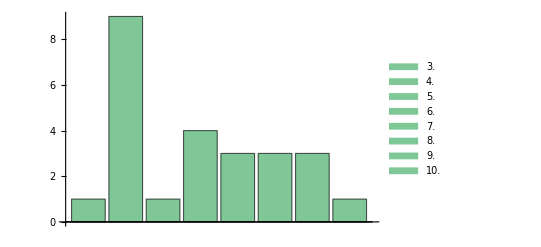

```mathematica
graf[tabela2, "število kobil", "starost v letih"]
```

Linijski prikaz

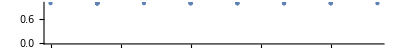

```mathematica
LinijskiPrikaz[tabela1, "starost"]
```

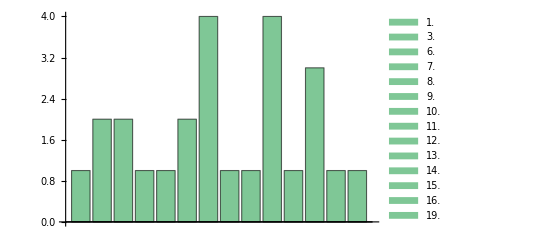
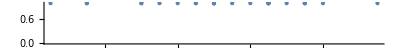
ŠTEVILO NASTOPOV V 2018
Grafičen prikaz
tabela3 = TableForm[Import["podatki.xlsx",{"Sheets","tabela3"}]]
"število štartov" | "število kobil"
1. | 1.
3. | 2.
6. | 2.
7. | 1.
8. | 1.
9. | 2.
10. | 4.
11. | 1.
12. | 1.
13. | 4.
14. | 1.
15. | 3.
16. | 1.
19. | 1.
graf[tabela3, "število kobil","število štartov"]
-Graphics-
Linijski prikaz
LinijskiPrikaz[tabela1, "število nastopov v 2018"]
-Graphics-

CELOTNO ŠTEVILO ŠTARTOV

Grafični prikaz

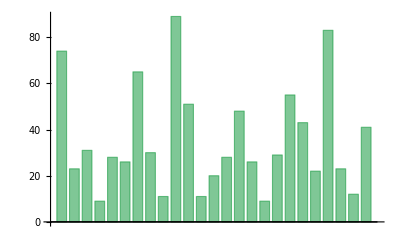

```mathematica
graf[tabela1, "celotno število štartov"]
```

Linijski prikaz

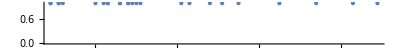

```mathematica
LinijskiPrikaz[tabela1, "celotno število štartov"]
```

UVRSTITEV NA 1. MESTO

Grafični prikaz

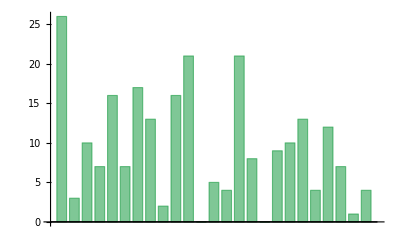

```mathematica
graf[tabela1, "uvrstitev na 1. mesto"]
```

Linijski prikaz

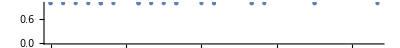

```mathematica
LinijskiPrikaz[tabela1, "uvrstitev na 1. mesto"]
```

UVRSTITEV NA 2. MESTO

Grafični prikaz

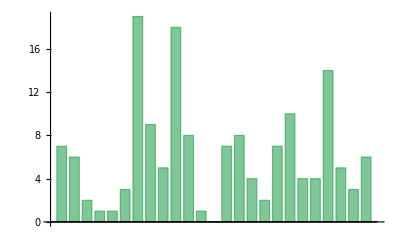

```mathematica
graf[tabela1, "uvrstitev na 2. mesto"]
```

Linijski prikaz

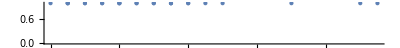

```mathematica
LinijskiPrikaz[tabela1, "uvrstitev na 2. mesto"]
```

UVRSTITEV NA 3. MESTO

Grafični prikaz

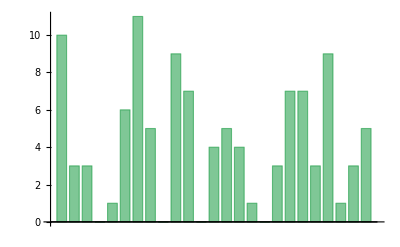

```mathematica
graf[tabela1, "uvrstitev na 3. mesto"]
```

Linijski prikaz

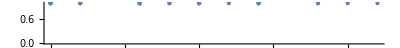

```mathematica
LinijskiPrikaz[tabela1, "uvrstitev na 3. mesto"]
```

# Prikaz steze

Konji tekmujejo na eni od treh različnih dolžin proge. Kratke steze imajo dolžino od 1600m do 1999m. Srednje dolge steze imajo dolžino 2000m do 2499 m, dolge steze pa imajo dolžino 2500 m in več.

```mathematica
Manipulate[Plot[y/.Solve[(x/a)^2+(y/3)^2==1],{x,-8, 8},AspectRatio->Automatic],{a,3,6}]
```

# Grafični prikazi

STAROST

Grafični prikaz

```mathematica
tabela2 = TableForm[Import["podatki.xlsx",{"Sheets","tabela2"}]]
```

starost v letih | število kobil
3. | 1.
4. | 9.
5. | 1.
6. | 4.
7. | 3.
8. | 3.
9. | 3.
10. | 1.

```mathematica
graf[tabela2, "število kobil", "starost v letih"]
```

-Graphics-

Linijski prikaz

```mathematica
LinijskiPrikaz[tabela1, "starost"]
```

-Graphics-

ŠTEVILO NASTOPOV V 2018
Grafičen prikaz
tabela3 = TableForm[Import["podatki.xlsx",{"Sheets","tabela3"}]]
"število štartov" | "število kobil"
1. | 1.
3. | 2.
6. | 2.
7. | 1.
8. | 1.
9. | 2.
10. | 4.
11. | 1.
12. | 1.
13. | 4.
14. | 1.
15. | 3.
16. | 1.
19. | 1.
graf[tabela3, "število kobil","število štartov"]
-Graphics-
Linijski prikaz
LinijskiPrikaz[tabela1, "število nastopov v 2018"]
-Graphics-

CELOTNO ŠTEVILO ŠTARTOV

Grafični prikaz

```mathematica
graf[tabela1, "celotno število štartov"]
```

-Graphics-

Linijski prikaz

```mathematica
LinijskiPrikaz[tabela1, "celotno število štartov"]
```

-Graphics-

UVRSTITEV NA 1. MESTO

Grafični prikaz

```mathematica
graf[tabela1, "uvrstitev na 1. mesto"]
```

-Graphics-

Linijski prikaz

```mathematica
LinijskiPrikaz[tabela1, "uvrstitev na 1. mesto"]
```

-Graphics-

UVRSTITEV NA 2. MESTO

Grafični prikaz

```mathematica
graf[tabela1, "uvrstitev na 2. mesto"]
```

-Graphics-

Linijski prikaz

```mathematica
LinijskiPrikaz[tabela1, "uvrstitev na 2. mesto"]
```

-Graphics-

UVRSTITEV NA 3. MESTO

Grafični prikaz

```mathematica
graf[tabela1, "uvrstitev na 3. mesto"]
```

-Graphics-

Linijski prikaz

```mathematica
LinijskiPrikaz[tabela1, "uvrstitev na 3. mesto"]
```

-Graphics-

# ZAKLJUČEK

To temo sem si izbrala, ker imam rada živali in sem na zgoraj navedni spletni nalogi tudi dobila dovolj podatkov za primerjavo ter statistično analizo. Seminarsko nalgoo sem nastavila tako, da če vstavimo podatke druge tabele, lahko z istimi definiranimi funkcijami poiščemo željenje podatke. S seminarsko nalogo sem se še bolj naučila  definirati funkcije in ukazovati programu Wolfram Alpha.